## 167Lu

```mathematica
ClearAll["Global`*"]
```

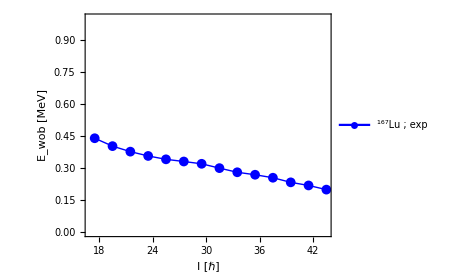

```mathematica
yrastEn=Sort[{15706,14459,13267,12132,11056,10040,9080.9,8154.9,7300.4,6501.5,5749.8,5048.0,4393.3,3786.5,3225.6,2720.5,2249.7}];
wob1En=Sort[{15282,14082,12933,11849,10817,9841,8917.8,8047.8,7231.8,6466.7,5755.7,5097.6,4492.6,3945.6}];
yrastSpin=Table[i/2,{i,25,89,4}];
wob1Spin=Table[i/2,{i,35,87,4}];
wobbling[yrast_,b1_,spins_]:=Table[{spins[[i]],b1[[i]]/1000-1/2(yrast[[i+2]]+yrast[[i+3]])/1000},{i,1,Length[b1]}];
data=wobbling[yrastEn,wob1En,wob1Spin];
fig=ListPlot[data,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{Thick,Blue},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{18,Bold,Black},PlotLegends->Placed[{Row[{Superscript["","167"],"Lu ; exp"}]},{0.3,0.9}],ImageSize->350,PlotRange->{Full,{0,1}}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/167Lu.pdf",fig];
Show[fig]
```